```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/john/topics/rubin

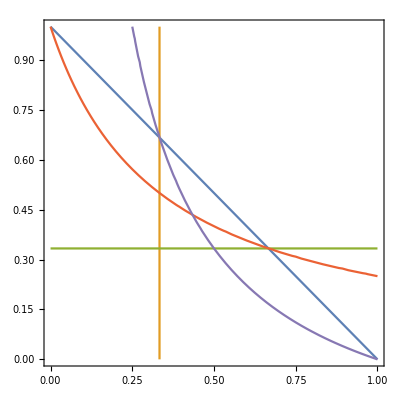

```mathematica
ch = 1.5; 
cm = 0.5;
ContourPlot[{q1 + q2==1,q1==cm/ch,q2==cm/ch,q1==(cm/ch)*(1-q2)/q2,q2==(cm/ch)*(1-q1)/q1}, {q1, 0,1}, {q2, 0,1}]
```

```mathematica
possible[q1_,q2_]:= {2*ch, ch + cm/q1, ch + cm/q2,  cm/(q1*q2), cm/q1 + cm/q2} 
sequences = {1->"(1)(2)", 2->"<1>(2)", 3->"(1)<2>", 4->"<1|2>", 5->"<1><2>"};
cost[q1_,q2_]:=Min[possible[q1,q2]]
Config[q1_,q2_]:=First@Flatten@Position[possible[q1,q2],cost[q1,q2]]
points = Flatten[Table[Table[{i, j}, {i, .01, 1-0.01, 0.1}], {j, 0.01, 1 - 0.01, 0.1}],1];
grouped = GatherBy[Map[{Config[#[[1]], #[[2]]],#}&, points],First];
Summarize[x_]:={Mean[Map[First[#]&,x]],Mean[Map[Last[#]&,x]]}
points = Map[Summarize,grouped];
labels=Style[Text[#[[1]]/.sequences,#[[2]]], Background->White]&/@points;
```

```mathematica
labels
```

{Text[(1)(2),{0.16,0.16}],Text[<1>(2),{0.641818,0.146364}],Text[<1|2>,{0.669459,0.669459}],Text[(1)<2>,{0.146364,0.641818}],Text[<1><2>,{0.443333,0.443333}]}

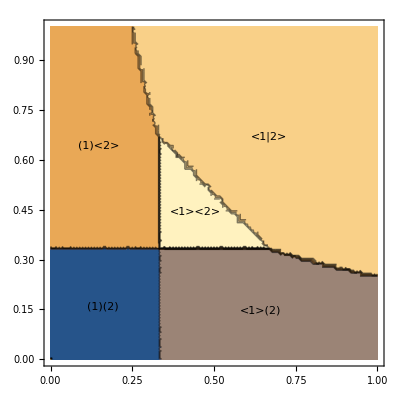

```mathematica
ContourPlot[Config[q1,q2],{q1,0,1},{q2,0,1},Epilog->labels]
```

```mathematica
Plot3D[cost[q1,q2],{q1,0,1},{q2,0,1},Epilog->labels]
```

-Graphics3D-

```mathematica
cm/ch
```

0.333333

```mathematica
Epilog->labels
```

```mathematica
lines = {Line[{{0,cm/ch},{1,cm/ch}}],Line[{{cm/ch,0},{cm/ch,1}}]};
```

```mathematica
callouts = {
Text["q_1=c_m/c_h",{cm/ch, 0.05}], 
Text["q_2=c_m/c_h",{ 0.1,cm/ch}]
};
```

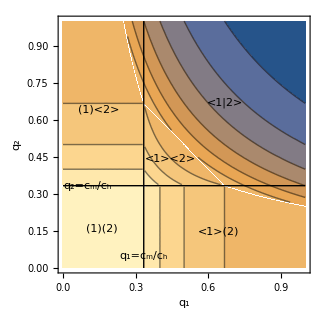

```mathematica
g=ContourPlot[cost[q1,q2],{q1,0,1},{q2,0,1},
AxesLabel->{"q1","q2"},Epilog->Append[Append[labels,lines],callouts],FrameLabel->{"q_1","q_2"}]
```

```mathematica
c=1/2
```

1/2

```mathematica
cost[0.8, 0.8]-cost[0.81, 0.8]
```

0.00964506

```mathematica
cost[0.8, 0.7]-cost[0.81, 0.7]
```

0.0110229

0.771605

```mathematica
Export["writeup/images/diagram.pdf", g, ImageSize->Medium]
```

writeup/images/diagram.pdf

```mathematica
?ContourPlot
```

```mathematica
?Gradient
```

```mathematica
cost[q1_,q2_]:=c/(q1*q2)
```

```mathematica
D[D[cost[q1,q2],q1],q2]
```

1/(2 q1^2 q2^2)

```mathematica
Gradient[cost[q1,q2]]
```

∇c/(q1 q2)

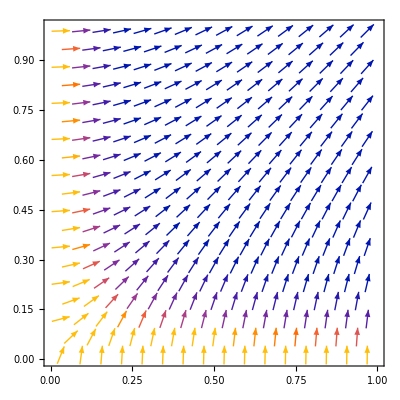

```mathematica
VectorPlot[{c/(q1^2 q2),c/(q1 q2^2)}/.c->1/2,{q1,0,1},{q2,0,1}]
```

```mathematica
{D[c/(q1*q2),q1],D[c/(q1*q2),q2]}
```

{-c/(q1^2 q2),-c/(q1 q2^2)}

```mathematica
{D[c/(q1*q2),q1],D[c/(q1*q2),q1]}/.{c->1,q1->1/2,q2->1/2}
```

{-8,-8}

```mathematica
D[c/(q1*q2),q2]
```

-c/(q1 q2^2)

```mathematica
?Gradient
```

```mathematica
D[D[c/(q1*q2),q1]]
```

-c/(q1^2 q2)

```mathematica
Sum[k*q*(1-q)^(k-1),{k,1,Infinity}]
```

1/q

```mathematica
Sum[k*q*(1-(r^(k-1))*q)^(k-1),{k,1,Infinity}]
```

$Aborted

```mathematica
?Export
```